```mathematica
Needs["AdvancedMapping`"]
```

```mathematica
BuildMatrix[paramList_,n_]:=Block[{parts},
parts = Partition[paramList,n-1];
Table[Insert[parts[[i]],1,i],{i,1,n}]
];
```

```mathematica
GeneratePossible[n_]:=Map[BuildMatrix[#,n]&,Tuples[{0,1},n(n-1)]];
```

```mathematica
CheckComplex[l_]:=Apply[Or,Map[MatchQ[#,_Complex]&,l]];
CheckNegative[l_]:=Apply[Or,Map[Re[#]≤0&,l]];

SelectDAG[matrices_,n_]:=Block[{eigenvalues,badPos,goodPos,output},
eigenvalues = Map[N[Eigenvalues[#]]&,matrices];
badPos = Position[eigenvalues,_?CheckNegative|_?CheckComplex];
goodPos = Delete[Range[Length[eigenvalues]],badPos];
output = Map[#-IdentityMatrix[n]&,matrices[[goodPos]]];
Return[output];
];
```

```mathematica
ListDAG[n_]:=Block[{possibleMatrices,dag},
possibleMatrices = GeneratePossible[n];
dag = SelectDAG[possibleMatrices,n];
Return[dag];
];
```

```mathematica
f[0]= 1;
f[1]= 1;
f[2]=3;
f[n_]:=Sum[(-1)^(i+1) Binomial[n,i] 2^(i(n-i))f[n-i],{i,1,n}];

PlotGraphs[n_]:=MapThread[
AdjacencyGraph[#1,
VertexLabels->"Name",
VertexShapeFunction->"Circle",
VertexSize->Small,
EdgeStyle->Thick,
PlotTheme->"LargeGraph",
PlotLabel->Style[Framed[ToString[#2]]],
ImageSize->{200,200}
]&,
{ListDAG[n],Range[f[n]]}
];
```

```mathematica
PlotGraphs[2]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotGraphs[3]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
graphDensity = Map[GraphDensity,PlotGraphs[3]]
```

{0,1/6,1/6,1/3,1/6,1/3,1/6,1/3,1/3,1/2,1/3,1/2,1/6,1/3,1/3,1/3,1/2,1/6,1/3,1/3,1/2,1/3,1/3,1/2,1/2}

```mathematica
graphDensity = Map[GraphDensity,PlotGraphs[4]];
```

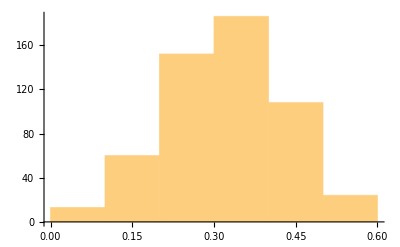

```mathematica
Histogram[graphDensity]
```

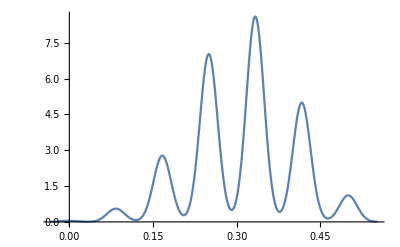

```mathematica
SmoothHistogram[graphDensity]
```

```mathematica
graphs = PlotGraphs[5];
```

```mathematica
graphDensity = Map[GraphDensity,graphs];
```

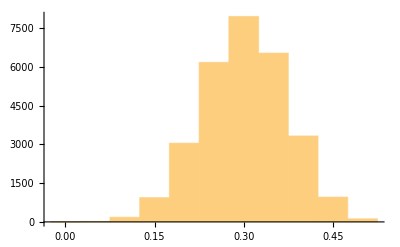

```mathematica
Histogram[graphDensity]
```

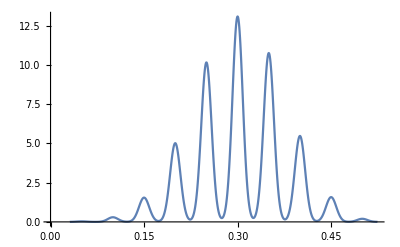

```mathematica
SmoothHistogram[graphDensity]
```

## Propiedades transformación grupo

```mathematica
m = ({{0, a, b}, {c, 0, d}, {e, f, 0}});
```

Prueba de que se puede permutar el grafo sin cambiar eigenvalores

Transformaciones que no alteran la determinante (ni los eigenvalores) cuando la diagonal es 1

```mathematica
NullTransform[ ({{a_, b_, c_}, {d_, e_, f_}, {g_, h_, i_}})]:= ({{a, b, c}, {d, e, f}, {g, h, i}});
T12[  ({{a_, b_, c_}, {d_, e_, f_}, {g_, h_, i_}})]:= ({{e, d, f}, {b, a, c}, {h, g, i}});
T13[  ({{a_, b_, c_}, {d_, e_, f_}, {g_, h_, i_}})]:= ({{i, h, g}, {f, e, d}, {c, b, a}});
T23[  ({{a_, b_, c_}, {d_, e_, f_}, {g_, h_, i_}})]:=  ({{a, c, b}, {g, i, h}, {d, f, e}});
```

```mathematica
start = ({{0, 0, 0}, {1, 0, 1}, {1, 0, 0}});
```

```mathematica
MatrixForm[T12[start]]
```

(0 | 1 | 1
0 | 0 | 0
0 | 1 | 0)

```mathematica
MatrixForm[T23[T12[start]]]
```

(0 | 1 | 1
0 | 0 | 1
0 | 0 | 0)

```mathematica
Eigenvalues[m+IdentityMatrix[3]]
```

{Root[-1+a c+b e-a d e-b c f+d f+(3-a c-b e-d f) #1-3 #1^2+#1^3&,1],Root[-1+a c+b e-a d e-b c f+d f+(3-a c-b e-d f) #1-3 #1^2+#1^3&,2],Root[-1+a c+b e-a d e-b c f+d f+(3-a c-b e-d f) #1-3 #1^2+#1^3&,3]}

```mathematica
Eigenvalues[T12[m+IdentityMatrix[3]]]
```

{Root[-1+a c+b e-a d e-b c f+d f+(3-a c-b e-d f) #1-3 #1^2+#1^3&,1],Root[-1+a c+b e-a d e-b c f+d f+(3-a c-b e-d f) #1-3 #1^2+#1^3&,2],Root[-1+a c+b e-a d e-b c f+d f+(3-a c-b e-d f) #1-3 #1^2+#1^3&,3]}

```mathematica
Eigenvalues[T13[m+IdentityMatrix[3]]]
```

{Root[-1+a c+b e-a d e-b c f+d f+(3-a c-b e-d f) #1-3 #1^2+#1^3&,1],Root[-1+a c+b e-a d e-b c f+d f+(3-a c-b e-d f) #1-3 #1^2+#1^3&,2],Root[-1+a c+b e-a d e-b c f+d f+(3-a c-b e-d f) #1-3 #1^2+#1^3&,3]}

```mathematica
Eigenvalues[T23[m+IdentityMatrix[3]]]
```

{Root[-1+a c+b e-a d e-b c f+d f+(3-a c-b e-d f) #1-3 #1^2+#1^3&,1],Root[-1+a c+b e-a d e-b c f+d f+(3-a c-b e-d f) #1-3 #1^2+#1^3&,2],Root[-1+a c+b e-a d e-b c f+d f+(3-a c-b e-d f) #1-3 #1^2+#1^3&,3]}

### Example

```mathematica
start = {{0,0,0},{1,0,0},{1,1,0}};
end = {{0,1,1},{0,0,1},{0,0,0}};
```

```mathematica
MatrixForm[start]
```

(0 | 0 | 0
1 | 0 | 0
1 | 1 | 0)

```mathematica
MatrixForm[end]
```

(0 | 1 | 1
0 | 0 | 1
0 | 0 | 0)

```mathematica
permutations = Map[
{#,Apply[Composition,#][start]}&,
Tuples[{T12,T13,T23,NullTransform},3]
];
indexes = Position[permutations[[All,2]],end]
Grid @ MapAt[MatrixForm,Extract[permutations,indexes],{All,2}]
```

{{7},{37}}

{T12,T13,T23} | (0 | 1 | 1
0 | 0 | 1
0 | 0 | 0)
{T23,T13,T12} | (0 | 1 | 1
0 | 0 | 1
0 | 0 | 0)

## Gráficas tarea

```mathematica
Graph[{1->2,2->3,2->4,3->4},VertexLabels->"Name",ImageSize->70]
```

```mathematica
MatrixForm[AdjacencyMatrix[{1->2,2->3,2->4,3->4}]]
```

(0 | 1 | 0 | 0
0 | 0 | 1 | 1
0 | 0 | 0 | 1
0 | 0 | 0 | 0)